```mathematica
CollectMPGEdges2[g_]:=Select[EdgeList[GraphComplement[g]],MaximalPlanarQ[VertexContract[g,{#[[1]],#[[2]]}]]&]
```

```mathematica
CollectMPGEdges2[g_]:=Select[EdgeList[GraphComplement[g]],PlanarGraphQ[VertexContract[g,{#[[1]],#[[2]]}]]&]
```

```mathematica
CollectMPGEdges2[ReadGrof[5]]
```

{1<->5,2<->4,7<->6}

```mathematica
CollectMPGEdges3[g_]:=Select[EdgeList[GraphComplement[g]],ChromaticPolynomial[VertexContract[g,{#[[1]],#[[2]]}],4]>0&]
```

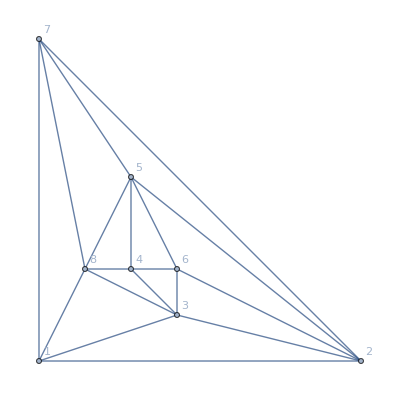

```mathematica
Graph[ReadGrof[18],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

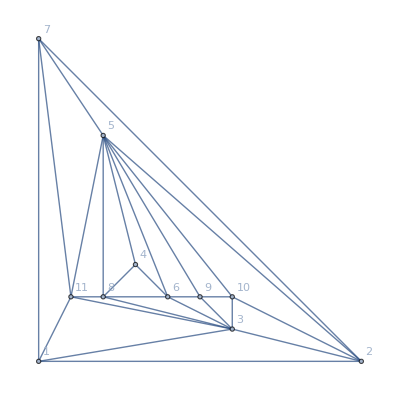

```mathematica
Graph[ReadGrof[500],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
Select[Table[k,{k,500}],CollectMPGEdges2[ReadGrof[#]]=={}&]
```

{1,18,36,38,40,41,45,46,91,94,107,108,109,120,121,122,146,159,170,171,172,175,187,188,196,197,202,205,206,207,208,210,214,215,216,218,219,220,221,222,223,224,233,235,298,299,340,378,403,405,407,408,437,442,457,458,478,479,482,485,486,489,490,500}

```mathematica
CollectMPGEdges[ReadGrof[4]]
```

{1<->2,1<->3,1<->5,1<->6,2<->3,2<->4,2<->6,3<->4,3<->5,4<->5,4<->6,5<->6}

```mathematica
Select[Table[k,{k,500}],CollectMPGEdges2[ReadGrof[#]]=={}&]
```

```mathematica
CollectMPGEdges2[Graph[plantri[[1]]]]
```

{}

```mathematica
Select[Table[k,{k,500}],CollectMPGEdges2[ReadGrof[#]]=={}&]
```

{1,18,36,38,40,41,45,46,91,94,107,108,109,120,121,122,146,159,170,171,172,175,187,188,196,197,202,205,206,207,208,210,214,215,216,218,219,220,221,222,223,224,233,235,298,299,340,378,403,405,407,408,437,442,457,458,478,479,482,485,486,489,490,500}

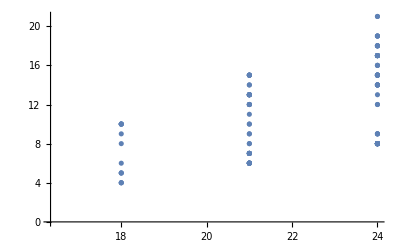

```mathematica
Table[With[{g=ReadGrof[k]},{EdgeCount[g],Length[CollectMPGEdges3[g]]}],{k,150}]//ListPlot
```

```mathematica
KnuthRep[SymbolToSets[v14x2x3x5]]
```

{1,2,3,1,4}

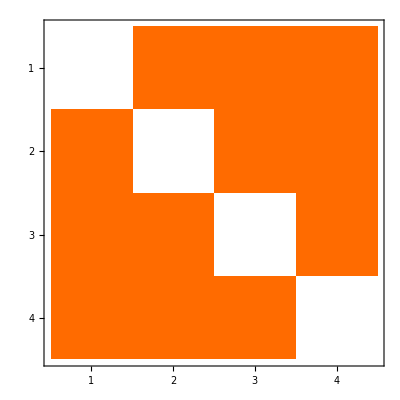
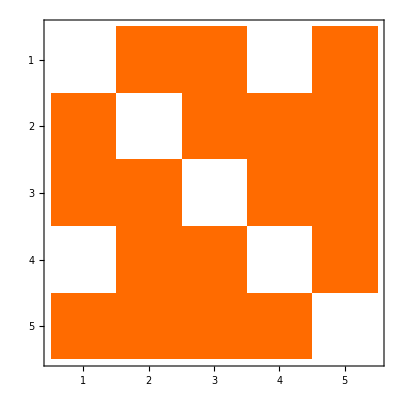
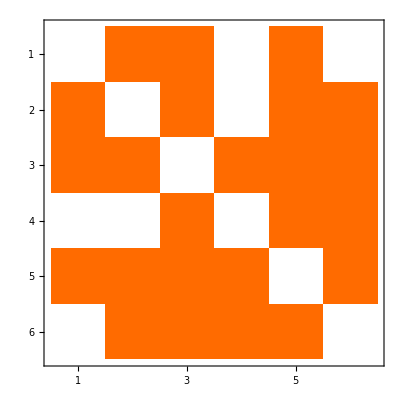
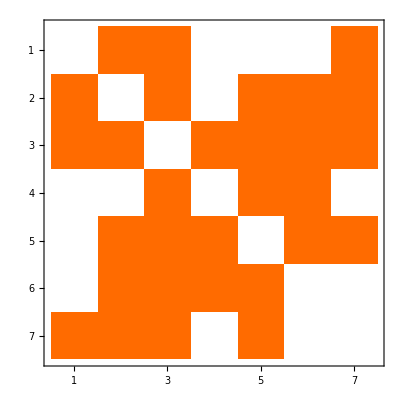
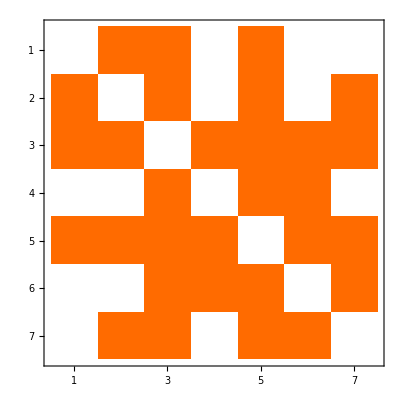
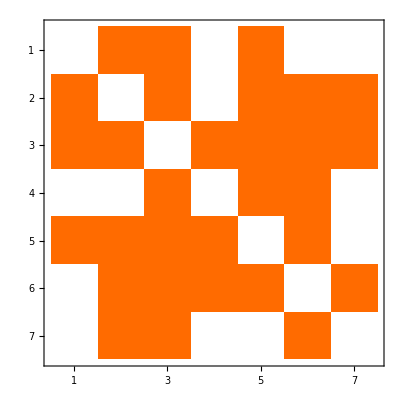
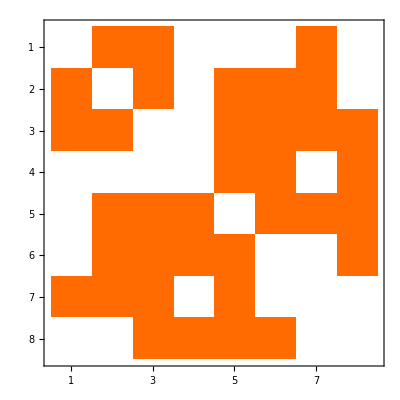
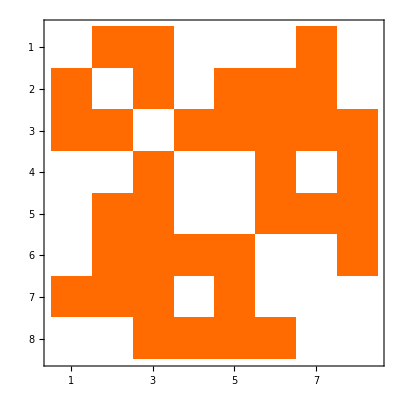
{-Graphics-{-Graphics-,{v1x2x3x4},{1,2,3,4}},-Graphics-{-Graphics-,{v14x2x3x5},{1,2,3,4,5}},-Graphics-{-Graphics-,{v16x24x3x5},{1,2,3,4,5,6}},-Graphics-{-Graphics-,{v15x24x3x67},{1,2,3,4,5,6,7}},-Graphics-{-Graphics-,{v147x26x3x5},{1,2,3,4,5,6,7}},-Graphics-{-Graphics-,{v16x24x3x57},{1,2,3,4,5,6,7}},-Graphics-{-Graphics-,{v15x28x34x67},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v145x28x3x67},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v15x26x3x478},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v158x24x3x67},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v15x24x38x67},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v178x246x3x5},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v16x24x38x57},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v15x26x34x789},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v145x28x39x67},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v15x28x39x467},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v167x28x34x59},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v159x28x34x67},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v15x28x349x67},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v15x289x34x67},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v145x26x3x789},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v159x28x3x467},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v167x28x3x459},{1,2,3,4,5,6,7,8,9}}}

```mathematica
Table[With[{h=ReadGrof[k]},
With[{g=Graph[Range[VertexCount[h]],Sort[EdgeList[h]],VertexLabels->"Name",ImageSize->80,GraphLayout->"PlanarEmbedding"]},
Labeled[MatrixPlot[AdjacencyMatrix[g]],{g,FindFullFormula4[g],VertexList[g]}]]],{k,Select[Range[50],ChromaticPolynomial[ReadGrof[#],4]==24&]}]
```

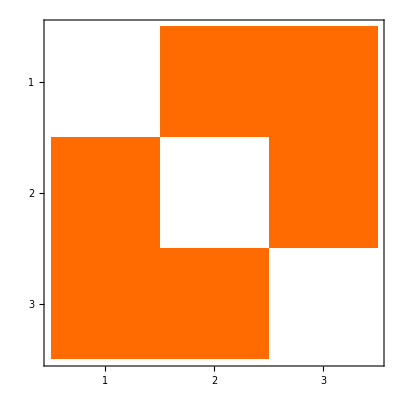
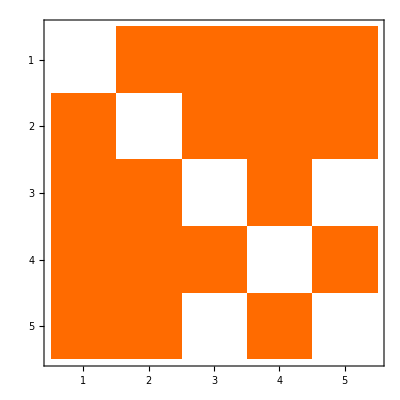
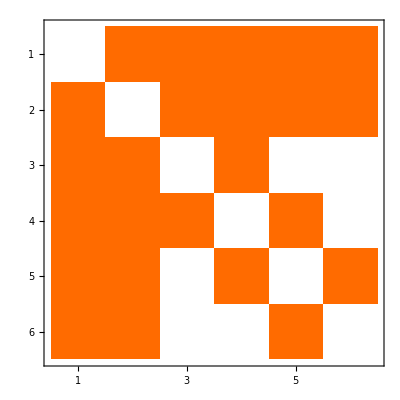
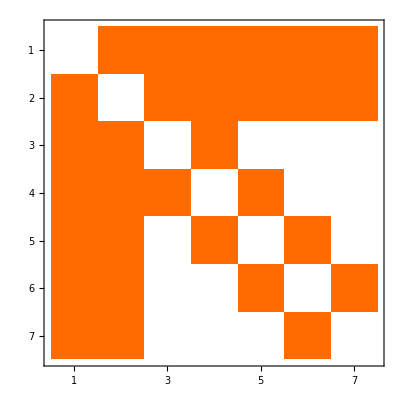
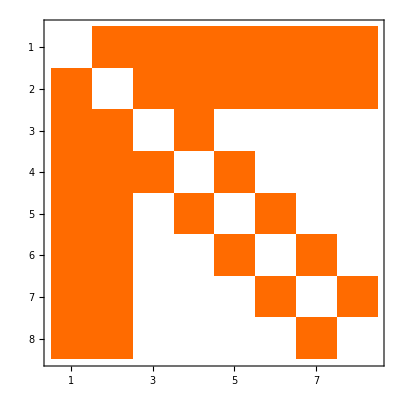
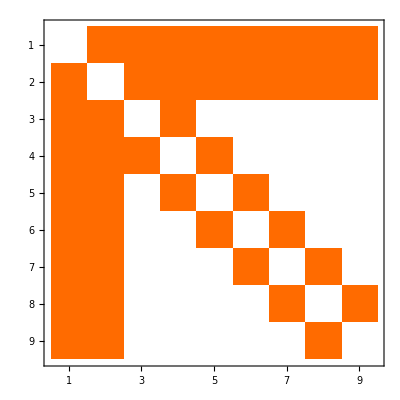
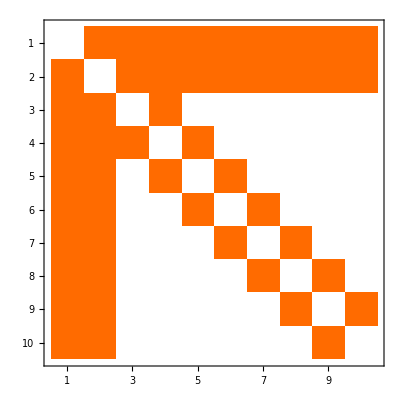
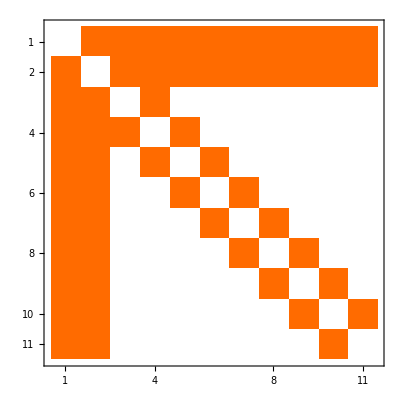
{-Graphics-{-Graphics-,{},{1,2,3}},-Graphics-{-Graphics-,{},{1,2,3}},-Graphics-{-Graphics-,{v1x2x3x4},{1,2,3,4}},-Graphics-{-Graphics-,{v1x2x35x4},{1,2,3,4,5}},-Graphics-{-Graphics-,{v1x2x35x46},{1,2,3,4,5,6}},-Graphics-{-Graphics-,{v1x2x357x46},{1,2,3,4,5,6,7}},-Graphics-{-Graphics-,{v1x2x357x468},{1,2,3,4,5,6,7,8}},-Graphics-{-Graphics-,{v1x2x3579x468},{1,2,3,4,5,6,7,8,9}},-Graphics-{-Graphics-,{v1x2x3579x468a},{1,2,3,4,5,6,7,8,9,10}},-Graphics-{-Graphics-,{v1x2x3579bx468a},{1,2,3,4,5,6,7,8,9,10,11}}}

```mathematica
Table[With[{h=MinimalGraph[k]},
With[{g=Graph[Range[VertexCount[h]],Sort[EdgeList[h]],VertexLabels->"Name",ImageSize->80,GraphLayout->"PlanarEmbedding"]},
Labeled[MatrixPlot[AdjacencyMatrix[g]],{g,FindFullFormula4[g],VertexList[g]}]]],{k,10}]
```

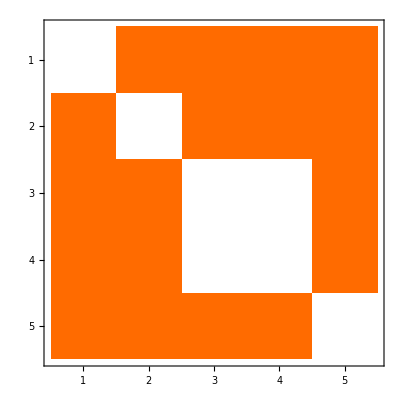
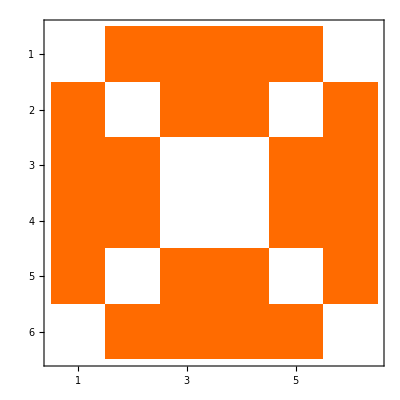
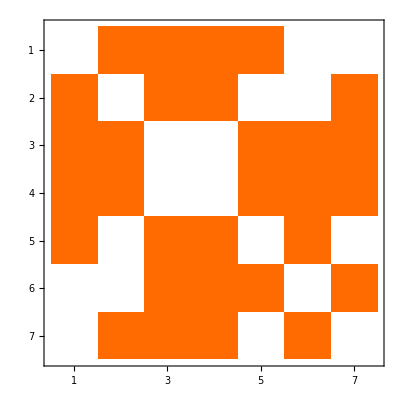
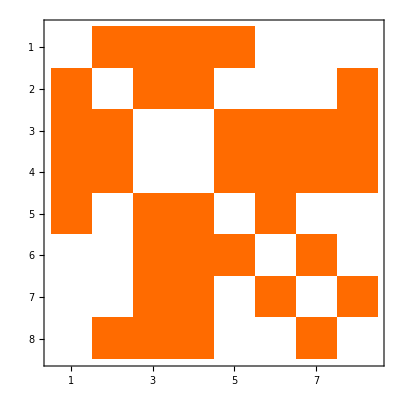
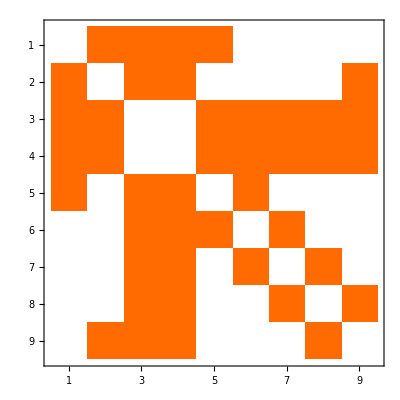
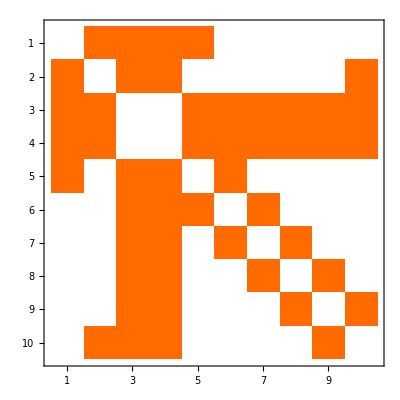
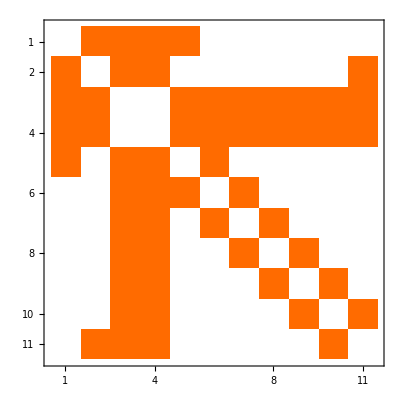
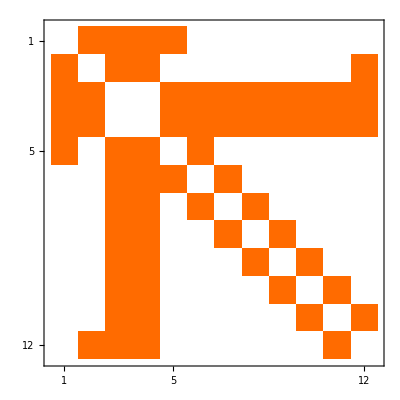
{-Graphics-{-Graphics-,{v1x2x34x5}},-Graphics-{-Graphics-,{v1x25x34x6,v16x2x34x5,v16x25x3x4}},-Graphics-{-Graphics-,{v1x26x34x57,v17x26x34x5,v17x25x34x6,v16x2x34x57,v16x25x34x7}},-Graphics-{-Graphics-,{v1x257x34x68,v18x26x34x57,v18x257x34x6,v17x26x34x58,v17x25x34x68,v168x2x34x57,v168x27x34x5,v16x27x34x58,v168x257x3x4,v168x25x34x7,v16x257x34x8}},-Graphics-{-Graphics-,{v1x268x34x579,v19x268x34x57,v19x257x34x68,v18x26x34x579,v18x257x34x69,v179x268x34x5,v17x268x34x59,v179x26x34x58,v179x258x34x6,v17x258x34x69,v179x25x34x68,v168x2x34x579,v16x28x34x579,v169x28x34x57,v168x27x34x59,v169x27x34x58,v169x258x34x7,v169x257x34x8,v168x257x34x9,v16x258x34x79,v168x25x34x79}},-Graphics-{-Graphics-,{v1x2579x34x68a,v1ax268x34x579,v1ax2579x34x68,v19x268x34x57a,v19x257x34x68a,v18ax26x34x579,v18x269x34x57a,v18ax269x34x57,v18ax2579x34x6,v18x2579x34x6a,v18ax257x34x69,v179x268x34x5a,v17ax268x34x59,v17x269x34x58a,v17ax269x34x58,v179x26x34x58a,v179x258x34x6a,v17ax258x34x69,v17x259x34x68a,v17ax259x34x68,v179x25x34x68a,v168ax2x34x579,v168x29x34x57a,v168ax29x34x57,v16ax28x34x579,v169x28x34x57a,v168ax279x34x5,v168x279x34x5a,v168ax27x34x59,v16x279x34x58a,v16ax279x34x58,v169x27x34x58a,v168ax2579x3x4,v168ax259x34x7,v168ax257x34x9,v169x257x34x8a,v169x258x34x7a,v168x259x34x7a,v16ax2579x34x8,v16ax258x34x79,v168x2579x34xa,v16x2579x34x8a,v168ax25x34x79}},-Graphics-{-Graphics-,{v1x268ax34x579b,v1bx268ax34x579,v1bx2579x34x68a,v1ax268x34x579b,v1ax2579x34x68b,v19bx268x34x57a,v19x268ax34x57b,v19bx268ax34x57,v19bx257x34x68a,v19x257ax34x68b,v19bx257ax34x68,v18bx26ax34x579,v18bx269x34x57a,v18ax269x34x57b,v18x26ax34x579b,v18ax26x34x579b,v18ax2579x34x6b,v18bx2579x34x6a,v18ax257x34x69b,v18x257ax34x69b,v18bx257ax34x69,v179bx268ax34x5,v179x268ax34x5b,v179bx268x34x5a,v17ax268x34x59b,v17x268ax34x59b,v17bx268ax34x59,v17bx269x34x58a,v17ax269x34x58b,v179x26ax34x58b,v179bx26x34x58a,v179bx26ax34x58,v179bx258ax34x6,v179x258ax34x6b,v179bx258x34x6a,v17ax258x34x69b,v17x258ax34x69b,v17bx258ax34x69,v17bx259x34x68a,v17ax259x34x68b,v179x25ax34x68b,v179bx25x34x68a,v179bx25ax34x68,v168ax2x34x579b,v168x2ax34x579b,v168bx2ax34x579,v168bx29x34x57a,v168ax29x34x57b,v16bx28ax34x579,v169x28ax34x57b,v169bx28x34x57a,v16x28ax34x579b,v169bx28ax34x57,v16ax28x34x579b,v168ax279x34x5b,v168bx279x34x5a,v168x27ax34x59b,v168bx27ax34x59,v168ax27x34x59b,v16bx279x34x58a,v16ax279x34x58b,v169x27ax34x58b,v169bx27x34x58a,v169bx27ax34x58,v169bx258ax34x7,v169bx257x34x8a,v168ax257x34x9b,v168ax259x34x7b,v169x258ax34x7b,v169bx257ax34x8,v169bx258x34x7a,v168x257ax34x9b,v168bx257ax34x9,v168bx259x34x7a,v169x257ax34x8b,v16ax258x34x79b,v168x25ax34x79b,v168bx2579x34xa,v168bx25ax34x79,v16ax2579x34x8b,v168ax2579x34xb,v16x258ax34x79b,v168ax25x34x79b,v16bx258ax34x79,v16bx2579x34x8a}},-Graphics-{-Graphics-,{v1x2579bx34x68ac,v1cx268ax34x579b,v1cx2579bx34x68a,v1bx268ax34x579c,v1bx2579x34x68ac,v1acx268x34x579b,v1acx268bx34x579,v1ax268bx34x579c,v1acx2579x34x68b,v1ax2579bx34x68c,v1acx2579bx34x68,v19bx268x34x57ac,v19cx268bx34x57a,v19x268bx34x57ac,v19cx268ax34x57b,v19bx268ax34x57c,v19bx257x34x68ac,v19cx257bx34x68a,v19x257bx34x68ac,v19cx257ax34x68b,v19bx257ax34x68c,v18acx26bx34x579,v18acx269x34x57b,v18bx269x34x57ac,v18bx26ax34x579c,v18ax26bx34x579c,v18cx269bx34x57a,v18cx26ax34x579b,v18ax269bx34x57c,v18x269bx34x57ac,v18acx26x34x579b,v18acx269bx34x57,v18acx2579bx34x6,v18ax2579bx34x6c,v18acx2579x34x6b,v18x2579bx34x6ac,v18cx2579bx34x6a,v18bx2579x34x6ac,v18acx257x34x69b,v18ax257bx34x69c,v18acx257bx34x69,v18cx257ax34x69b,v18bx257ax34x69c,v179bx268ax34x5c,v179cx268ax34x5b,v179bx268x34x5ac,v179x268bx34x5ac,v179cx268bx34x5a,v17acx268x34x59b,v17ax268bx34x59c,v17acx268bx34x59,v17cx268ax34x59b,v17bx268ax34x59c,v17acx269x34x58b,v17bx269x34x58ac,v179x26bx34x58ac,v179cx26bx34x58a,v179cx26ax34x58b,v17cx269bx34x58a,v179bx26ax34x58c,v17ax269bx34x58c,v17x269bx34x58ac,v17acx269bx34x58,v179bx26x34x58ac,v179bx258ax34x6c,v179cx258ax34x6b,v179bx258x34x6ac,v179x258bx34x6ac,v179cx258bx34x6a,v17acx258x34x69b,v17ax258bx34x69c,v17acx258bx34x69,v17cx258ax34x69b,v17bx258ax34x69c,v17acx259x34x68b,v17bx259x34x68ac,v179x25bx34x68ac,v179cx25bx34x68a,v179cx25ax34x68b,v17cx259bx34x68a,v179bx25ax34x68c,v17ax259bx34x68c,v17x259bx34x68ac,v17acx259bx34x68,v179bx25x34x68ac,v168acx2x34x579b,v168acx2bx34x579,v168ax2bx34x579c,v168cx2ax34x579b,v168bx2ax34x579c,v168x29bx34x57ac,v168cx29bx34x57a,v168bx29x34x57ac,v168acx29x34x57b,v168ax29bx34x57c,v168acx29bx34x57,v16acx28bx34x579,v169x28bx34x57ac,v169cx28bx34x57a,v169cx28ax34x57b,v16bx28ax34x579c,v16ax28bx34x579c,v169bx28ax34x57c,v16cx28ax34x579b,v16acx28x34x579b,v169bx28x34x57ac,v168acx279bx34x5,v168ax279bx34x5c,v168acx279x34x5b,v168x279bx34x5ac,v168cx279bx34x5a,v168bx279x34x5ac,v168cx27ax34x59b,v168bx27ax34x59c,v168acx27x34x59b,v168ax27bx34x59c,v168acx27bx34x59,v16acx279x34x58b,v16bx279x34x58ac,v169x27bx34x58ac,v169cx27bx34x58a,v169cx27ax34x58b,v16cx279bx34x58a,v169bx27ax34x58c,v16ax279bx34x58c,v16x279bx34x58ac,v16acx279bx34x58,v169bx27x34x58ac,v168acx2579bx3x4,v168acx259bx34x7,v169bx257x34x8ac,v168acx257x34x9b,v169bx258ax34x7c,v168ax259bx34x7c,v168acx257bx34x9,v168acx259x34x7b,v169x257bx34x8ac,v169cx258ax34x7b,v169cx257bx34x8a,v168ax257bx34x9c,v169bx258x34x7ac,v168x259bx34x7ac,v169bx257ax34x8c,v168cx259bx34x7a,v168cx257ax34x9b,v168bx259x34x7ac,v169x258bx34x7ac,v169cx258bx34x7a,v169cx257ax34x8b,v168bx257ax34x9c,v16acx2579bx34x8,v16acx258x34x79b,v168x2579bx34xac,v168cx2579bx34xa,v168cx25ax34x79b,v16ax2579bx34x8c,v168bx25ax34x79c,v16ax258bx34x79c,v16acx258bx34x79,v16acx2579x34x8b,v168bx2579x34xac,v168acx2579x34xb,v168acx25x34x79b,v16cx258ax34x79b,v168ax2579bx34xc,v16x2579bx34x8ac,v168ax25bx34x79c,v168acx25bx34x79,v16cx2579bx34x8a,v16bx2579x34x8ac,v16bx258ax34x79c}},-Graphics-{-Graphics-,{v1x268acx34x579bd,v1dx268acx34x579b,v1dx2579bx34x68ac,v1cx268ax34x579bd,v1cx2579bx34x68ad,v1bdx268acx34x579,v1bx268acx34x579d,v1bdx268ax34x579c,v1bdx2579cx34x68a,v1bx2579cx34x68ad,v1bdx2579x34x68ac,v1acx268x34x579bd,v1ax268cx34x579bd,v1adx268cx34x579b,v1acx268bx34x579d,v1adx268bx34x579c,v1adx2579cx34x68b,v1adx2579bx34x68c,v1acx2579bx34x68d,v1ax2579cx34x68bd,v1acx2579x34x68bd,v19bdx268x34x57ac,v19bdx268cx34x57a,v19bx268cx34x57ad,v19cx268bx34x57ad,v19dx268bx34x57ac,v19dx268acx34x57b,v19bx268acx34x57d,v19bdx268ax34x57c,v19x268acx34x57bd,v19bdx268acx34x57,v19cx268ax34x57bd,v19bdx257x34x68ac,v19bdx257cx34x68a,v19bx257cx34x68ad,v19cx257bx34x68ad,v19dx257bx34x68ac,v19dx257acx34x68b,v19bx257acx34x68d,v19bdx257ax34x68c,v19x257acx34x68bd,v19bdx257acx34x68,v19cx257ax34x68bd,v18bdx26acx34x579,v18bdx269x34x57ac,v18acx269x34x57bd,v18acx26bx34x579d,v18bx26acx34x579d,v18bdx269cx34x57a,v18bdx26ax34x579c,v18ax269cx34x57bd,v18adx269cx34x57b,v18adx26bx34x579c,v18bx269cx34x57ad,v18cx26ax34x579bd,v18ax26cx34x579bd,v18adx269bx34x57c,v18adx26cx34x579b,v18cx269bx34x57ad,v18x26acx34x579bd,v18acx26x34x579bd,v18acx269bx34x57d,v18dx26acx34x579b,v18dx269bx34x57ac,v18acx2579bx34x6d,v18adx2579bx34x6c,v18ax2579cx34x6bd,v18adx2579cx34x6b,v18acx2579x34x6bd,v18dx2579bx34x6ac,v18cx2579bx34x6ad,v18bx2579cx34x6ad,v18bdx2579x34x6ac,v18bdx2579cx34x6a,v18acx257x34x69bd,v18ax257cx34x69bd,v18adx257cx34x69b,v18adx257bx34x69c,v18acx257bx34x69d,v18dx257acx34x69b,v18bx257acx34x69d,v18bdx257ax34x69c,v18x257acx34x69bd,v18bdx257acx34x69,v18cx257ax34x69bd,v179bdx268acx34x5,v179bx268acx34x5d,v179bdx268ax34x5c,v179x268acx34x5bd,v179dx268acx34x5b,v179cx268ax34x5bd,v179bdx268x34x5ac,v179bx268cx34x5ad,v179bdx268cx34x5a,v179dx268bx34x5ac,v179cx268bx34x5ad,v17acx268x34x59bd,v17ax268cx34x59bd,v17adx268cx34x59b,v17adx268bx34x59c,v17acx268bx34x59d,v17dx268acx34x59b,v17bx268acx34x59d,v17bdx268ax34x59c,v17x268acx34x59bd,v17bdx268acx34x59,v17cx268ax34x59bd,v17bdx269x34x58ac,v17acx269x34x58bd,v179x26acx34x58bd,v179dx26acx34x58b,v179dx26bx34x58ac,v17bdx269cx34x58a,v179cx26ax34x58bd,v17ax269cx34x58bd,v17adx269cx34x58b,v179cx26bx34x58ad,v17bx269cx34x58ad,v179bdx26cx34x58a,v179bdx26ax34x58c,v17adx269bx34x58c,v179bx26cx34x58ad,v17cx269bx34x58ad,v17acx269bx34x58d,v179bx26acx34x58d,v179bdx26x34x58ac,v179bdx26acx34x58,v17dx269bx34x58ac,v179bdx258acx34x6,v179bx258acx34x6d,v179bdx258ax34x6c,v179x258acx34x6bd,v179dx258acx34x6b,v179cx258ax34x6bd,v179bdx258x34x6ac,v179bx258cx34x6ad,v179bdx258cx34x6a,v179dx258bx34x6ac,v179cx258bx34x6ad,v17acx258x34x69bd,v17ax258cx34x69bd,v17adx258cx34x69b,v17adx258bx34x69c,v17acx258bx34x69d,v17dx258acx34x69b,v17bx258acx34x69d,v17bdx258ax34x69c,v17x258acx34x69bd,v17bdx258acx34x69,v17cx258ax34x69bd,v17bdx259x34x68ac,v17acx259x34x68bd,v179x25acx34x68bd,v179dx25acx34x68b,v179dx25bx34x68ac,v17bdx259cx34x68a,v179cx25ax34x68bd,v17ax259cx34x68bd,v17adx259cx34x68b,v179cx25bx34x68ad,v17bx259cx34x68ad,v179bdx25cx34x68a,v179bdx25ax34x68c,v17adx259bx34x68c,v179bx25cx34x68ad,v17cx259bx34x68ad,v17acx259bx34x68d,v179bx25acx34x68d,v179bdx25x34x68ac,v179bdx25acx34x68,v17dx259bx34x68ac,v168acx2x34x579bd,v168ax2cx34x579bd,v168adx2cx34x579b,v168acx2bx34x579d,v168adx2bx34x579c,v168x2acx34x579bd,v168dx2acx34x579b,v168cx2ax34x579bd,v168bdx2acx34x579,v168bx2acx34x579d,v168bdx2ax34x579c,v168dx29bx34x57ac,v168cx29bx34x57ad,v168bdx29cx34x57a,v168bx29cx34x57ad,v168bdx29x34x57ac,v168adx29cx34x57b,v168adx29bx34x57c,v168acx29bx34x57d,v168ax29cx34x57bd,v168acx29x34x57bd,v16bdx28acx34x579,v169x28acx34x57bd,v169dx28acx34x57b,v16acx28bx34x579d,v169dx28bx34x57ac,v16bx28acx34x579d,v16bdx28ax34x579c,v169cx28ax34x57bd,v16adx28bx34x579c,v169cx28bx34x57ad,v169bdx28cx34x57a,v169bdx28ax34x57c,v16cx28ax34x579bd,v16ax28cx34x579bd,v16adx28cx34x579b,v169bx28cx34x57ad,v16x28acx34x579bd,v16acx28x34x579bd,v169bx28acx34x57d,v169bdx28x34x57ac,v169bdx28acx34x57,v16dx28acx34x579b,v168acx279bx34x5d,v168adx279bx34x5c,v168acx279x34x5bd,v168ax279cx34x5bd,v168adx279cx34x5b,v168dx279bx34x5ac,v168cx279bx34x5ad,v168bdx279x34x5ac,v168bx279cx34x5ad,v168bdx279cx34x5a,v168x27acx34x59bd,v168dx27acx34x59b,v168cx27ax34x59bd,v168bdx27ax34x59c,v168bx27acx34x59d,v168bdx27acx34x59,v168adx27cx34x59b,v168adx27bx34x59c,v168acx27bx34x59d,v168ax27cx34x59bd,v168acx27x34x59bd,v16bdx279x34x58ac,v16acx279x34x58bd,v169x27acx34x58bd,v169dx27acx34x58b,v169dx27bx34x58ac,v16bdx279cx34x58a,v169cx27ax34x58bd,v16ax279cx34x58bd,v16adx279cx34x58b,v169cx27bx34x58ad,v16bx279cx34x58ad,v169bdx27cx34x58a,v169bdx27ax34x58c,v16adx279bx34x58c,v169bx27cx34x58ad,v16cx279bx34x58ad,v16acx279bx34x58d,v169bx27acx34x58d,v169bdx27x34x58ac,v169bdx27acx34x58,v16dx279bx34x58ac,v169bdx258acx34x7,v169bdx257x34x8ac,v168acx257x34x9bd,v169bx258acx34x7d,v168acx259bx34x7d,v168ax257cx34x9bd,v169bx257cx34x8ad,v168adx259bx34x7c,v169bdx258ax34x7c,v169bdx257cx34x8a,v168adx257cx34x9b,v168acx259x34x7bd,v169x258acx34x7bd,v169dx257bx34x8ac,v169dx258acx34x7b,v168acx257bx34x9d,v169cx257bx34x8ad,v169cx258ax34x7bd,v168ax259cx34x7bd,v168adx259cx34x7b,v168adx257bx34x9c,v169bdx257acx34x8,v169bdx258x34x7ac,v168x257acx34x9bd,v168dx259bx34x7ac,v169bx257acx34x8d,v168dx257acx34x9b,v168cx257ax34x9bd,v169bx258cx34x7ad,v168cx259bx34x7ad,v169bdx258cx34x7a,v169bdx257ax34x8c,v168bdx257acx34x9,v168bdx259x34x7ac,v169x257acx34x8bd,v169dx258bx34x7ac,v169dx257acx34x8b,v168bx257acx34x9d,v169cx257ax34x8bd,v169cx258bx34x7ad,v168bx259cx34x7ad,v168bdx259cx34x7a,v168bdx257ax34x9c,v16acx258x34x79bd,v168x25acx34x79bd,v168dx25acx34x79b,v16acx2579bx34x8d,v168dx2579bx34xac,v168cx25ax34x79bd,v16ax258cx34x79bd,v16adx258cx34x79b,v16adx2579bx34x8c,v168cx2579bx34xad,v168bdx2579cx34xa,v168bdx25ax34x79c,v16ax2579cx34x8bd,v16adx258bx34x79c,v16adx2579cx34x8b,v168bx2579cx34xad,v16acx2579x34x8bd,v16acx258bx34x79d,v168bx25acx34x79d,v168bdx25acx34x79,v168bdx2579x34xac,v168adx2579cx34xb,v168adx25cx34x79b,v16dx258acx34x79b,v168adx2579bx34xc,v16dx2579bx34x8ac,v168adx25bx34x79c,v168acx2579bx34xd,v16cx2579bx34x8ad,v168acx25bx34x79d,v16bx2579cx34x8ad,v16bx258acx34x79d,v16bdx2579x34x8ac,v16bdx258ax34x79c,v16x258acx34x79bd,v16bdx258acx34x79,v16bdx2579cx34x8a,v168ax2579cx34xbd,v168ax25cx34x79bd,v168acx25x34x79bd,v16cx258ax34x79bd,v168acx2579x34xbd}},-Graphics-{-Graphics-,{v1x2579bdx34x68ace,v1ex268acx34x579bd,v1ex2579bdx34x68ac,v1dx268acx34x579be,v1dx2579bx34x68ace,v1cex268ax34x579bd,v1cx268adx34x579be,v1cex268adx34x579b,v1cex2579bdx34x68a,v1cx2579bdx34x68ae,v1cex2579bx34x68ad,v1bdx268acx34x579e,v1bex268acx34x579d,v1bx268adx34x579ce,v1bex268adx34x579c,v1bdx268ax34x579ce,v1bdx2579cx34x68ae,v1bex2579cx34x68ad,v1bx2579dx34x68ace,v1bex2579dx34x68ac,v1bdx2579x34x68ace,v1acex268x34x579bd,v1acx268dx34x579be,v1acex268dx34x579b,v1aex268cx34x579bd,v1adx268cx34x579be,v1acex268bdx34x579,v1acx268bdx34x579e,v1acex268bx34x579d,v1ax268bdx34x579ce,v1aex268bdx34x579c,v1adx268bx34x579ce,v1acex2579dx34x68b,v1acex2579bx34x68d,v1adx2579bx34x68ce,v1adx2579cx34x68be,v1acx2579dx34x68be,v1aex2579bdx34x68c,v1aex2579cx34x68bd,v1acx2579bdx34x68e,v1ax2579bdx34x68ce,v1acex2579bdx34x68,v1acex2579x34x68bd,v19bdx268x34x57ace,v19bx268dx34x57ace,v19bex268dx34x57ac,v19bdx268cx34x57ae,v19bex268cx34x57ad,v19cex268bdx34x57a,v19cx268bdx34x57ae,v19cex268bx34x57ad,v19x268bdx34x57ace,v19ex268bdx34x57ac,v19dx268bx34x57ace,v19cex268adx34x57b,v19bx268adx34x57ce,v19bex268adx34x57c,v19bex268acx34x57d,v19dx268acx34x57be,v19cx268adx34x57be,v19bdx268acx34x57e,v19ex268acx34x57bd,v19cex268ax34x57bd,v19bdx268ax34x57ce,v19bdx257x34x68ace,v19bx257dx34x68ace,v19bex257dx34x68ac,v19bdx257cx34x68ae,v19bex257cx34x68ad,v19cex257bdx34x68a,v19cx257bdx34x68ae,v19cex257bx34x68ad,v19x257bdx34x68ace,v19ex257bdx34x68ac,v19dx257bx34x68ace,v19cex257adx34x68b,v19bx257adx34x68ce,v19bex257adx34x68c,v19bex257acx34x68d,v19dx257acx34x68be,v19cx257adx34x68be,v19bdx257acx34x68e,v19ex257acx34x68bd,v19cex257ax34x68bd,v19bdx257ax34x68ce,v18acex26bdx34x579,v18bdx269x34x57ace,v18acex269x34x57bd,v18bdx26acx34x579e,v18acx26bdx34x579e,v18acex269dx34x57b,v18acex26bx34x579d,v18bx269dx34x57ace,v18bex26acx34x579d,v18bex269dx34x57ac,v18acx269dx34x57be,v18bdx26ax34x579ce,v18ax26bdx34x579ce,v18bdx269cx34x57ae,v18aex26bdx34x579c,v18aex269cx34x57bd,v18adx26bx34x579ce,v18bx26adx34x579ce,v18bex26adx34x579c,v18bex269cx34x57ad,v18adx269cx34x57be,v18cex269bdx34x57a,v18cex26ax34x579bd,v18ax269bdx34x57ce,v18aex269bdx34x57c,v18aex26cx34x579bd,v18cx269bdx34x57ae,v18adx26cx34x579be,v18cx26adx34x579be,v18cex26adx34x579b,v18cex269bx34x57ad,v18adx269bx34x57ce,v18acex26x34x579bd,v18ex26acx34x579bd,v18acex269bx34x57d,v18x269bdx34x57ace,v18acx26dx34x579be,v18acx269bdx34x57e,v18acex269bdx34x57,v18ex269bdx34x57ac,v18acex26dx34x579b,v18dx26acx34x579be,v18dx269bx34x57ace,v18acex2579bdx34x6,v18acx2579bdx34x6e,v18acex2579bx34x6d,v18ax2579bdx34x6ce,v18aex2579bdx34x6c,v18adx2579bx34x6ce,v18aex2579cx34x6bd,v18adx2579cx34x6be,v18acex2579x34x6bd,v18acx2579dx34x6be,v18acex2579dx34x6b,v18cex2579bx34x6ad,v18dx2579bx34x6ace,v18bx2579dx34x6ace,v18bex2579dx34x6ac,v18bex2579cx34x6ad,v18ex2579bdx34x6ac,v18bdx2579cx34x6ae,v18cx2579bdx34x6ae,v18x2579bdx34x6ace,v18cex2579bdx34x6a,v18bdx2579x34x6ace,v18acex257x34x69bd,v18acex257dx34x69b,v18acx257dx34x69be,v18aex257cx34x69bd,v18adx257cx34x69be,v18ax257bdx34x69ce,v18aex257bdx34x69c,v18adx257bx34x69ce,v18acex257bx34x69d,v18acx257bdx34x69e,v18acex257bdx34x69,v18cex257adx34x69b,v18bx257adx34x69ce,v18bex257adx34x69c,v18bex257acx34x69d,v18dx257acx34x69be,v18cx257adx34x69be,v18bdx257acx34x69e,v18ex257acx34x69bd,v18cex257ax34x69bd,v18bdx257ax34x69ce,v179bdx268acx34x5e,v179bex268acx34x5d,v179bx268adx34x5ce,v179bex268adx34x5c,v179bdx268ax34x5ce,v179ex268acx34x5bd,v179dx268acx34x5be,v179cex268ax34x5bd,v179cx268adx34x5be,v179cex268adx34x5b,v179bdx268x34x5ace,v179bex268dx34x5ac,v179bx268dx34x5ace,v179bex268cx34x5ad,v179bdx268cx34x5ae,v179x268bdx34x5ace,v179ex268bdx34x5ac,v179dx268bx34x5ace,v179cex268bx34x5ad,v179cx268bdx34x5ae,v179cex268bdx34x5a,v17acex268x34x59bd,v17acex268dx34x59b,v17acx268dx34x59be,v17aex268cx34x59bd,v17adx268cx34x59be,v17ax268bdx34x59ce,v17aex268bdx34x59c,v17adx268bx34x59ce,v17acex268bx34x59d,v17acx268bdx34x59e,v17acex268bdx34x59,v17cex268adx34x59b,v17bx268adx34x59ce,v17bex268adx34x59c,v17bex268acx34x59d,v17dx268acx34x59be,v17cx268adx34x59be,v17bdx268acx34x59e,v17ex268acx34x59bd,v17cex268ax34x59bd,v17bdx268ax34x59ce,v17bdx269x34x58ace,v17acex269x34x58bd,v179x26bdx34x58ace,v179ex26bdx34x58ac,v179ex26acx34x58bd,v17acex269dx34x58b,v179dx26bx34x58ace,v17bx269dx34x58ace,v17bex269dx34x58ac,v17acx269dx34x58be,v179dx26acx34x58be,v179cex26bdx34x58a,v179cex26ax34x58bd,v17bdx269cx34x58ae,v17aex269cx34x58bd,v179cx26bdx34x58ae,v179cex26adx34x58b,v179cex26bx34x58ad,v17bex269cx34x58ad,v17adx269cx34x58be,v179cx26adx34x58be,v17cex269bdx34x58a,v179bdx26ax34x58ce,v17ax269bdx34x58ce,v17aex269bdx34x58c,v179bdx26cx34x58ae,v17cx269bdx34x58ae,v179bex26adx34x58c,v179bex26cx34x58ad,v17cex269bx34x58ad,v17adx269bx34x58ce,v179bx26adx34x58ce,v179bex26acx34x58d,v17acex269bx34x58d,v17x269bdx34x58ace,v17acx269bdx34x58e,v179bx26dx34x58ace,v17acex269bdx34x58,v179bex26dx34x58ac,v17ex269bdx34x58ac,v179bdx26x34x58ace,v179bdx26acx34x58e,v17dx269bx34x58ace,v179bdx258acx34x6e,v179bex258acx34x6d,v179bx258adx34x6ce,v179bex258adx34x6c,v179bdx258ax34x6ce,v179ex258acx34x6bd,v179dx258acx34x6be,v179cex258ax34x6bd,v179cx258adx34x6be,v179cex258adx34x6b,v179bdx258x34x6ace,v179bex258dx34x6ac,v179bx258dx34x6ace,v179bex258cx34x6ad,v179bdx258cx34x6ae,v179x258bdx34x6ace,v179ex258bdx34x6ac,v179dx258bx34x6ace,v179cex258bx34x6ad,v179cx258bdx34x6ae,v179cex258bdx34x6a,v17acex258x34x69bd,v17acex258dx34x69b,v17acx258dx34x69be,v17aex258cx34x69bd,v17adx258cx34x69be,v17ax258bdx34x69ce,v17aex258bdx34x69c,v17adx258bx34x69ce,v17acex258bx34x69d,v17acx258bdx34x69e,v17acex258bdx34x69,v17cex258adx34x69b,v17bx258adx34x69ce,v17bex258adx34x69c,v17bex258acx34x69d,v17dx258acx34x69be,v17cx258adx34x69be,v17bdx258acx34x69e,v17ex258acx34x69bd,v17cex258ax34x69bd,v17bdx258ax34x69ce,v17bdx259x34x68ace,v17acex259x34x68bd,v179x25bdx34x68ace,v179ex25bdx34x68ac,v179ex25acx34x68bd,v17acex259dx34x68b,v179dx25bx34x68ace,v17bx259dx34x68ace,v17bex259dx34x68ac,v17acx259dx34x68be,v179dx25acx34x68be,v179cex25bdx34x68a,v179cex25ax34x68bd,v17bdx259cx34x68ae,v17aex259cx34x68bd,v179cx25bdx34x68ae,v179cex25adx34x68b,v179cex25bx34x68ad,v17bex259cx34x68ad,v17adx259cx34x68be,v179cx25adx34x68be,v17cex259bdx34x68a,v179bdx25ax34x68ce,v17ax259bdx34x68ce,v17aex259bdx34x68c,v179bdx25cx34x68ae,v17cx259bdx34x68ae,v179bex25adx34x68c,v179bex25cx34x68ad,v17cex259bx34x68ad,v17adx259bx34x68ce,v179bx25adx34x68ce,v179bex25acx34x68d,v17acex259bx34x68d,v17x259bdx34x68ace,v17acx259bdx34x68e,v179bx25dx34x68ace,v17acex259bdx34x68,v179bex25dx34x68ac,v17ex259bdx34x68ac,v179bdx25x34x68ace,v179bdx25acx34x68e,v17dx259bx34x68ace,v168acex2x34x579bd,v168acx2dx34x579be,v168acex2dx34x579b,v168aex2cx34x579bd,v168adx2cx34x579be,v168acex2bdx34x579,v168acx2bdx34x579e,v168acex2bx34x579d,v168ax2bdx34x579ce,v168aex2bdx34x579c,v168adx2bx34x579ce,v168ex2acx34x579bd,v168dx2acx34x579be,v168cex2ax34x579bd,v168cx2adx34x579be,v168cex2adx34x579b,v168bdx2acx34x579e,v168bex2acx34x579d,v168bx2adx34x579ce,v168bex2adx34x579c,v168bdx2ax34x579ce,v168x29bdx34x57ace,v168ex29bdx34x57ac,v168dx29bx34x57ace,v168cex29bdx34x57a,v168cx29bdx34x57ae,v168cex29bx34x57ad,v168bdx29cx34x57ae,v168bex29cx34x57ad,v168bx29dx34x57ace,v168bex29dx34x57ac,v168bdx29x34x57ace,v168acex29dx34x57b,v168acex29bx34x57d,v168adx29bx34x57ce,v168adx29cx34x57be,v168acx29dx34x57be,v168aex29bdx34x57c,v168aex29cx34x57bd,v168acx29bdx34x57e,v168acex29x34x57bd,v168acex29bdx34x57,v168ax29bdx34x57ce,v16acex28bdx34x579,v169x28bdx34x57ace,v16bdx28acx34x579e,v16acx28bdx34x579e,v169ex28bdx34x57ac,v169ex28acx34x57bd,v169dx28bx34x57ace,v16acex28bx34x579d,v16bex28acx34x579d,v169dx28acx34x57be,v169cex28bdx34x57a,v16bdx28ax34x579ce,v169cex28ax34x57bd,v16ax28bdx34x579ce,v16aex28bdx34x579c,v169cx28bdx34x57ae,v169cex28adx34x57b,v16adx28bx34x579ce,v169cex28bx34x57ad,v16bx28adx34x579ce,v16bex28adx34x579c,v169cx28adx34x57be,v16cex28ax34x579bd,v169bdx28ax34x57ce,v16aex28cx34x579bd,v169bdx28cx34x57ae,v169bex28adx34x57c,v16adx28cx34x579be,v169bex28cx34x57ad,v16cx28adx34x579be,v16cex28adx34x579b,v169bx28adx34x57ce,v16acex28x34x579bd,v169bex28acx34x57d,v16ex28acx34x579bd,v16acx28dx34x579be,v169bx28dx34x57ace,v169bex28dx34x57ac,v16acex28dx34x579b,v169bdx28x34x57ace,v16dx28acx34x579be,v169bdx28acx34x57e,v168acex279bdx34x5,v168acx279bdx34x5e,v168acex279bx34x5d,v168ax279bdx34x5ce,v168aex279bdx34x5c,v168adx279bx34x5ce,v168acex279x34x5bd,v168acx279dx34x5be,v168acex279dx34x5b,v168aex279cx34x5bd,v168adx279cx34x5be,v168x279bdx34x5ace,v168ex279bdx34x5ac,v168dx279bx34x5ace,v168cex279bx34x5ad,v168cx279bdx34x5ae,v168cex279bdx34x5a,v168bdx279x34x5ace,v168bex279dx34x5ac,v168bx279dx34x5ace,v168bex279cx34x5ad,v168bdx279cx34x5ae,v168ex27acx34x59bd,v168dx27acx34x59be,v168cex27ax34x59bd,v168cex27adx34x59b,v168cx27adx34x59be,v168bdx27ax34x59ce,v168bex27adx34x59c,v168bx27adx34x59ce,v168bex27acx34x59d,v168bdx27acx34x59e,v168acex27dx34x59b,v168acex27bx34x59d,v168adx27bx34x59ce,v168adx27cx34x59be,v168acx27dx34x59be,v168aex27bdx34x59c,v168aex27cx34x59bd,v168acx27bdx34x59e,v168acex27x34x59bd,v168acex27bdx34x59,v168ax27bdx34x59ce,v16bdx279x34x58ace,v16acex279x34x58bd,v169x27bdx34x58ace,v169ex27bdx34x58ac,v169ex27acx34x58bd,v16acex279dx34x58b,v169dx27bx34x58ace,v16bx279dx34x58ace,v16bex279dx34x58ac,v16acx279dx34x58be,v169dx27acx34x58be,v169cex27bdx34x58a,v169cex27ax34x58bd,v16bdx279cx34x58ae,v16aex279cx34x58bd,v169cx27bdx34x58ae,v169cex27adx34x58b,v169cex27bx34x58ad,v16bex279cx34x58ad,v16adx279cx34x58be,v169cx27adx34x58be,v16cex279bdx34x58a,v169bdx27ax34x58ce,v16ax279bdx34x58ce,v16aex279bdx34x58c,v169bdx27cx34x58ae,v16cx279bdx34x58ae,v169bex27adx34x58c,v169bex27cx34x58ad,v16cex279bx34x58ad,v16adx279bx34x58ce,v169bx27adx34x58ce,v169bex27acx34x58d,v16acex279bx34x58d,v16x279bdx34x58ace,v16acx279bdx34x58e,v169bx27dx34x58ace,v16acex279bdx34x58,v169bex27dx34x58ac,v16ex279bdx34x58ac,v169bdx27x34x58ace,v169bdx27acx34x58e,v16dx279bx34x58ace,v168acex2579bdx3x4,v168acex259bdx34x7,v168acex257x34x9bd,v169bdx257x34x8ace,v169bdx258acx34x7e,v168acx259bdx34x7e,v169bex257dx34x8ac,v169bex258acx34x7d,v168acx257dx34x9be,v169bx257dx34x8ace,v168acex259bx34x7d,v168acex257dx34x9b,v168aex257cx34x9bd,v169bex257cx34x8ad,v169bx258adx34x7ce,v168ax259bdx34x7ce,v168aex259bdx34x7c,v169bex258adx34x7c,v168adx257cx34x9be,v169bdx257cx34x8ae,v168adx259bx34x7ce,v169bdx258ax34x7ce,v168acex257bdx34x9,v168acex259x34x7bd,v169x257bdx34x8ace,v169ex257bdx34x8ac,v169ex258acx34x7bd,v168acx257bdx34x9e,v169dx258acx34x7be,v168acx259dx34x7be,v169dx257bx34x8ace,v168acex259dx34x7b,v168acex257bx34x9d,v169cex257bx34x8ad,v168aex259cx34x7bd,v169cex258ax34x7bd,v168ax257bdx34x9ce,v169cx257bdx34x8ae,v169cx258adx34x7be,v169cex258adx34x7b,v169cex257bdx34x8a,v168aex257bdx34x9c,v168adx257bx34x9ce,v168adx259cx34x7be,v169bdx258x34x7ace,v168x259bdx34x7ace,v168ex259bdx34x7ac,v168ex257acx34x9bd,v169bdx257acx34x8e,v169bex258dx34x7ac,v168dx257acx34x9be,v169bex257acx34x8d,v169bx258dx34x7ace,v168dx259bx34x7ace,v168cex257ax34x9bd,v168cex259bx34x7ad,v169bex258cx34x7ad,v168cx257adx34x9be,v169bx257adx34x8ce,v168cx259bdx34x7ae,v168cex259bdx34x7a,v169bex257adx34x8c,v168cex257adx34x9b,v169bdx257ax34x8ce,v169bdx258cx34x7ae,v168bdx259x34x7ace,v169x258bdx34x7ace,v169ex258bdx34x7ac,v169ex257acx34x8bd,v168bdx257acx34x9e,v168bex259dx34x7ac,v169dx257acx34x8be,v168bex257acx34x9d,v169dx258bx34x7ace,v168bx259dx34x7ace,v169cex257ax34x8bd,v168bex259cx34x7ad,v169cex258bx34x7ad,v168bx257adx34x9ce,v169cx257adx34x8be,v169cx258bdx34x7ae,v169cex258bdx34x7a,v169cex257adx34x8b,v168bex257adx34x9c,v168bdx257ax34x9ce,v168bdx259cx34x7ae,v16acex2579bdx34x8,v16acex258x34x79bd,v168x2579bdx34xace,v16acx2579bdx34x8e,v168ex25acx34x79bd,v168ex2579bdx34xac,v16acex258dx34x79b,v168dx2579bx34xace,v16acex2579bx34x8d,v16acx258dx34x79be,v168dx25acx34x79be,v168cex2579bdx34xa,v168cex25ax34x79bd,v16ax2579bdx34x8ce,v16aex258cx34x79bd,v16aex2579bdx34x8c,v168cx2579bdx34xae,v168cex25adx34x79b,v16adx2579bx34x8ce,v168cex2579bx34xad,v16adx258cx34x79be,v168cx25adx34x79be,v168bdx25ax34x79ce,v16ax258bdx34x79ce,v16aex258bdx34x79c,v16aex2579cx34x8bd,v168bdx2579cx34xae,v168bex25adx34x79c,v16adx2579cx34x8be,v168bex2579cx34xad,v16adx258bx34x79ce,v168bx25adx34x79ce,v16acex2579x34x8bd,v168bex25acx34x79d,v16acex258bx34x79d,v168bx2579dx34xace,v16acx2579dx34x8be,v16acx258bdx34x79e,v16acex258bdx34x79,v16acex2579dx34x8b,v168bex2579dx34xac,v168bdx2579x34xace,v168bdx25acx34x79e,v168acex2579dx34xb,v16cex258adx34x79b,v168acex25dx34x79b,v168acex2579bx34xd,v16cex2579bx34x8ad,v168acex25bx34x79d,v168adx25bx34x79ce,v168adx2579bx34xce,v16dx2579bx34x8ace,v16bx2579dx34x8ace,v16bx258adx34x79ce,v16bex2579dx34x8ac,v16bex258adx34x79c,v16bex2579cx34x8ad,v16bex258acx34x79d,v168adx2579cx34xbe,v168adx25cx34x79be,v16dx258acx34x79be,v168acx2579dx34xbe,v16cx258adx34x79be,v168acx25dx34x79be,v168aex2579bdx34xc,v16ex2579bdx34x8ac,v168aex25bdx34x79c,v16bdx2579cx34x8ae,v16bdx258acx34x79e,v168aex2579cx34xbd,v168aex25cx34x79bd,v16ex258acx34x79bd,v168acx2579bdx34xe,v16cx2579bdx34x8ae,v168acx25bdx34x79e,v16x2579bdx34x8ace,v16cex258ax34x79bd,v16cex2579bdx34x8a,v16bdx258ax34x79ce,v16bdx2579x34x8ace,v168acex25x34x79bd,v168acex25bdx34x79,v168ax25bdx34x79ce,v168acex2579x34xbd,v168ax2579bdx34xce}}}

```mathematica
Table[With[{h=JacobsThalGraph[k]},
With[{g=Graph[Range[VertexCount[h]],Sort[EdgeList[h]],VertexLabels->"Name",ImageSize->80,GraphLayout->"PlanarEmbedding"]},
Labeled[MatrixPlot[AdjacencyMatrix[g]],{Graph[g,GraphHighlight->CollectMPGEdges[g]],FindFullFormula4[g]}]]],{k,10}]
```